```mathematica
Remove["Global`*"]

l[z_]=(2 c/Ho)(1-1/Sqrt[1+z])
dz=D[l[z],z]
dτ=ne σ (1+z)^3 (dz/(1+z))
t[z_]= Integrate[dτ,{z,0,z},Assumptions->z>0]//FullSimplify
ρ=3.8*^-31;
σ=6.65*^-25;
mp=1.67*^-24;
ne= ρ/mp;
c=2.998*^10;
Ho=2.3*^-18;
Solve[t[z]==1,z]
(*Integrate[ne σ c (1+z)^3(Ho (1+z)^(3/2))^-1(1+z)^-1,z,Assumptions->z>0]
Integrate[ne σ c (1+z)^3(Ho (1+z)^(3/2))^-1(1+z)^-1,{z,0,z},Assumptions->z>0]
t[z_]=%
Solve[t[z]==1,z]*)
```

(2 c (1-1/(√(1+z))))/Ho

c/(Ho (1+z)^(3/2))

(c ne √(1+z) σ)/Ho

(2 c ne (-1+√(1+z)+z √(1+z)) σ)/(3 Ho)

{{z→82.3898}}

```mathematica
Remove["Global`*"]
(*Curve of Growth*)
Solve[{A to^(2/3)+ B to^-1==1,(2/3)A to^(-1/3)-B to^-2==0},{A,B}]
```

{{A→3/(5 to^(2/3)),B→(2 to)/5}}

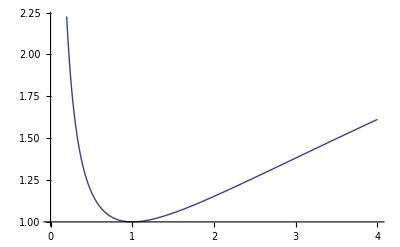

```mathematica
Plot[(3/5)t^(2/3)+(2/5)t^-1,{t,0,4}]
```

```mathematica
Remove["Global`*"]
dlow[x_]=1+3/x+(3 √(1+x))/x^(3/2)Log[√(1+x)-√x]
dcrit[z_]=3/5(1/(1+z))+2/5(1/(1+z))^(-3/2)//N
xz=(1-Ωm)/((1+z)Ωm)
Ωm=.3;
dlow[z_]=dlow[xz];

dlow[0]
dlow[1]
%%/%
dcrit[0]
dcrit[1]
%%/%
```

1+3/x+(3 √(1+x) Log[-√x+√(1+x)])/x^(3/2)

0.4/(1/(1.+z))^(3/2)+0.6/(1.+z)

(1-Ωm)/((1+z) Ωm)

0.42638

0.288246

1.47922

1.

1.43137

0.698631

(6.42857+1.92857 z-2.94594 √(1+z) √(1+2.33333/(1+z))+(-4.92857+3.22651 √(1+z) √(1+2.33333/(1+z))+z (-1.92857+1.26255 √(1+z) √(1+2.33333/(1+z)))) Log[-1.52753/(√(1+z))+√(1+2.33333/(1+z))])/(3.33333+1. z-1.52753 √(1+z) √(1+2.33333/(1+z)))

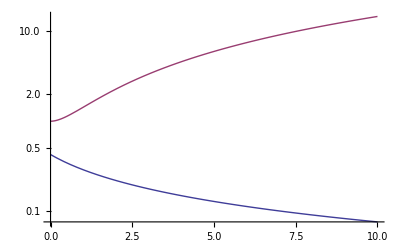

```mathematica
Clear[ddlow,ddcrit]
ddlow[z_]=D[dlow[z],z] //PowerExpand//FullSimplify
ddcrit[z_]=D[dcrit[z],z];
LogPlot[{Abs[dlow[z]],Abs[dcrit[z]]},{z,0,10}]
```

```mathematica
ddlow[-5]
```

-0.149134+6.93889×10^-17 ⅈ

```mathematica
Series[dcrit[z],{z,0,2}]
```

1.+0.5 z+0.625 z^2+O[z]^3

```mathematica
Remove["Global`*"]
Rat[z_]=(1+z)*(5Ωm)/2(Ωm^(4/7)-ΩΛ+(1+Ωm/2)(1+ΩΛ/70))^-1
Ωm=.3;ΩΛ=.7
Rat[99]
```

(5 (1+z) Ωm)/(2 (Ωm^(4/7)+(1+Ωm/2) (1+ΩΛ/70)-ΩΛ))

0.7

77.7937